# Studio della cinematica di una gru per scarico/carico navi

Si consideri una delle due gru della foto (matricole pari destra, dispari sinistra). Ricavare delle misure ragionevoli dalla fotografia (almeno le proporzioni).

## Analisi di Posizione

#### Funzione Quadrilatero

```mathematica
Quadrilatero[q_,xA_,yA_,L1_,L2_,L3_,modo_,xD_,yD_]:= Module[{xB,yB,L5,θ5,cosα,α,θ2,xC,yC,θ3},
xB =xA+L1 Cos[q]; (* si calcola la posizione di B *)
yB = yA+L1 Sin[q];
L5 = √((xD-xB)^2+(yD-yB)^2); (* si calcola la lunghezza del lato BD *)
θ5 = ArcTan[xD-xB,yD-yB]; (* si calcola l'angolo θ5: notare l'uso della funzione arcotangente a due argomenti *)
cosα= (L5^2+L2^2-L3^2)/(2 L5 L2); (* teorema del coseno: si calcola l'argomento del coseno *)
α = 1;
If[Abs[cosα]≤1,
If[modo>0,α =1,α = -1] (* meccanismo si assembla *)
,
If[modo>0,α =1,α = -1] (* non si assembla e α è un numero complesso *)
];
θ2 = θ5-α*ArcCos[cosα]; (* si calcola θ2 *)
xC= xB + L2 Cos[θ2]; (* si trova il punto C *)
yC= yB + L2 Sin[θ2];
θ3 = ArcTan[xD-xC,yD-yC]; (* si calcola θ3: notare l'uso della funzione arcotangente a due argomenti *)
{θ2,θ3,{{xA,yA},{xB,yB},{xC,yC},{xD,yD}}} (* si restituisce θ3,θ2 e il poligono ABCD *)
]
```

#### Funzione Trilatero per Estremo P e Peso K

```mathematica
Trilatero[θ1_,θ2_,LA_,LB_,xC_,yC_]:= {{LA Cos[θ1],LA Sin[θ1]},{LA Cos[θ1]+LB Cos[θ2],LA Sin[θ1]+LB Sin[θ2]},{xC,yC}}
```

#### Definizione Valori

```mathematica
var=
{xA=0,
yA=0,
L1=10,
L2=13,
L6=5,
xD=-7.5,
yD=13,
L3=25,
L4=5,
L5=30,
L1P=18,
L2P=25,
L1K=10,
L2K=10,
θ1noto=π/6,
θ2noto=π/6,
θ0=ArcTan[xD,yD],
L0=√(xD^2+yD^2)};
modo1=-1;
modo2=1;
v1=1;
v2=2;
```

#### Determino le posizini dei qudrilateri

```mathematica
Pol1[pol1_]:=Quadrilatero[pol1,xA,yA,Lv1,Lv2,Lv6,modo2,xvD,yvD]
Pol2[pol2_]:=Quadrilatero[pol2,
							Pol1[pol2][[3,2,1]],
							Pol1[pol2][[3,2,2]],Lv3,Lv4,Lv5,modo2,
							Pol1[pol2][[3,3,1]],
							Pol1[pol2][[3,3,2]]]
```

#### Posizione P

```mathematica
Pol3[pol3_]:=Trilatero[pol3,Pol2[pol3][[1]]+π+θ1noto,Lv1+Lv3,L1P,
						Pol2[pol3][[3,3,1]],Pol2[pol3][[3,3,2]]		
						]
```

#### Posizione Peso k

```mathematica
Pol4[pol4_]:=Trilatero[ArcTan[xvD,yvD],Pol1[pol4][[2]]-θ2noto,√(xvD^2+yvD^2),L1K,Pol1[pol4][[3,3,1]],Pol1[pol4][[3,3,2]]]
```

#### Traiettoria e Distanze Max e Min

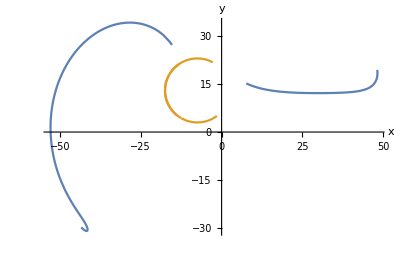

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]},{Pol4[q][[2,1]],Pol4[q][[2,2]]}},{q,0,2π},AxesLabel->{"x","y"}]]
```

```mathematica
Manipulate[Block[{Lv1=l1,Lv2=l2,Lv3=l3,Lv4=l4,Lv5=l5,Lv6=l6,xvD=XD,yvD=YD},ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]},{Pol4[q][[2,1]],Pol4[q][[2,2]]}},{q,0,2π},PlotRange->{{-60,60},{-10,40}}]],{l1,10,20,0.1},{l2,10,20,0.1},{l3,20,30,0.1},{l4,2,10,0.1},{l5,20,40,0.1},{l6,2,10,0.1},{XD,-15,0,0.1},{YD,1,15,0.1}]
```

```mathematica
L11=12.2;
L22=13.7;
L33=23.8;
L44=5.2;
L55=33.9;
L66=6.6;
xDD=-11;
yDD=8.7;
```

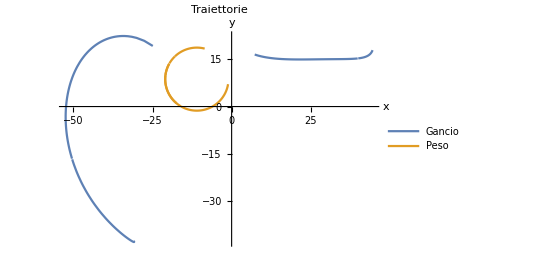

```mathematica
Block[{Lv1=L11,Lv2=L22,Lv3=L33,Lv4=L44,Lv5=L55,Lv6=L66,xvD=xDD,yvD=yDD},ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]},{Pol4[q][[2,1]],Pol4[q][[2,2]]}},{q,0,2π},AxesLabel->{"x","y"},PlotLabel->"Traiettorie",PlotLegends->{"Gancio","Peso"}]]
```

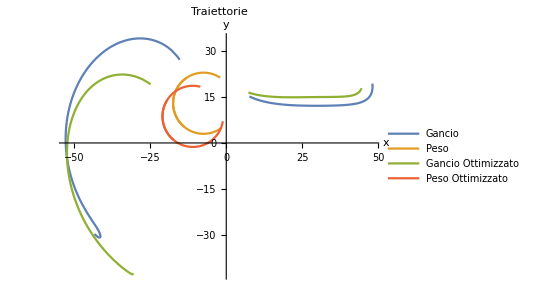

```mathematica
ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]}/.{Lv1-> L1,Lv2-> L2,Lv3-> L3,Lv4-> L4,Lv5-> L5,Lv6-> L6,xvD-> xD,yvD-> yD},{Pol4[q][[2,1]],Pol4[q][[2,2]]}/.{Lv1-> L1,Lv2-> L2,Lv3-> L3,Lv4-> L4,Lv5-> L5,Lv6-> L6,xvD-> xD,yvD-> yD},{Pol3[q][[2,1]],Pol3[q][[2,2]]}/.{Lv1-> L11,Lv2-> L22,Lv3-> L33,Lv4-> L44,Lv5-> L55,Lv6-> L66,xvD-> xDD,yvD-> yDD},{Pol4[q][[2,1]],Pol4[q][[2,2]]}/.{Lv1-> L11,Lv2-> L22,Lv3-> L33,Lv4-> L44,Lv5-> L55,Lv6-> L66,xvD-> xDD,yvD-> yDD}},{q,0,2π},AxesLabel->{"x","y"},PlotLabel->"Traiettorie",PlotLegends->{"Gancio","Peso","Gancio Ottimizzato","Peso Ottimizzato"}]
```

```mathematica
L1=L11;
L2=L22;
L3=L33;
L4=L44;
L5=L55;
L6=L66;
xD=xDD;
yD=yDD;
```

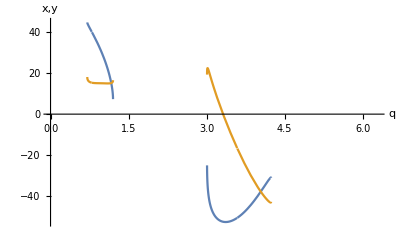

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Plot[{Pol3[q][[2,1]],Pol3[q][[2,2]]},{q,0,2π},AxesLabel->{"q","x,y"}]]
```

```mathematica
qmax=0;
qmin=π/2;
Timing@Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Do[If[Pol3[i][[2,1]]∈Reals,
											If[i>qmax,qmax=i,0],0],{i,0,π/2,π/36000}]]
Timing@Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Do[If[Pol3[π/2-i][[2,1]]∈Reals,
											If[π/2-i<qmin,qmin=π/2-i,0],0],{i,0,π/2,π/36000}]]
```

{42.4531,Null}

{42.5,Null}

```mathematica
qmax
```

(4589 π)/12000

```mathematica
qmin
```

(8089 π)/36000

```mathematica
domQ=FunctionDomain[Pol3[q][[2,2]],q];
```

```mathematica
miny=Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},FindMinimum[{Pol3[q][[2,2]],domQ},{q,π/3}]]
```

{14.9397,{q→1.10163}}

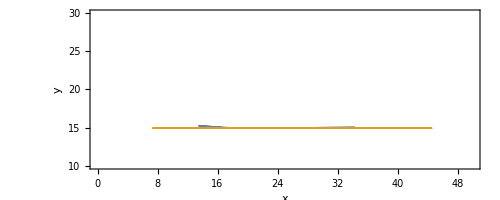

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]},{r,miny[[1]]}},{q,0,π/2},{r,Pol3[qmin][[2,1]],Pol3[qmax][[2,1]]},PlotRange->{{0,50},{10,30}},AxesLabel->{"x","y"}]]
```

La traiettoria va da dx a sx al variare di q

```mathematica
diffsx=Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Pol3[qmax][[2,2]]-miny[[1]]]
```

1.55785

```mathematica
diffdx=Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Pol3[qmin][[2,2]]-miny[[1]]]
```

3.02837

```mathematica
point=Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Array[Pol3[#][[2,2]]&,500,{qmin,qmax}]];
```

```mathematica
mediana=Median[point]
```

15.0512

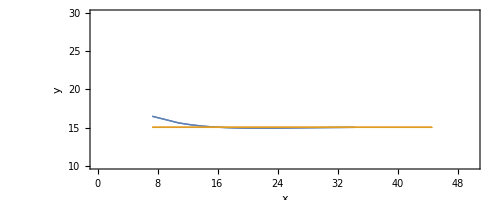

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]},{r,mediana}},{q,qmin,qmax},{r,Pol3[qmin][[2,1]],Pol3[qmax][[2,1]]},PlotRange->{{0,50},{10,30}},AxesLabel->{"x","y"}]]
```

```mathematica
deviazione=StandardDeviation[point]
```

0.426381

Retta piu piana possibile

```mathematica
pointpiano=Array[Pol3[#][[2,2]]&,500,{0,π/2}];
```

```mathematica
(*Timing@Solve[StandardDeviation[pointpiano]≤5,{Lv1,Lv2,Lv3,Lv4,Lv5,Lv6}]*)
```

## Analisi di Velocità

#### Rapporto Velocità Gancio/Velocità Peso

```mathematica
τPyq=D[Pol3[q][[2,2]], q];
```

```mathematica
τKyq=D[Pol4[q][[2,2]], q];
```

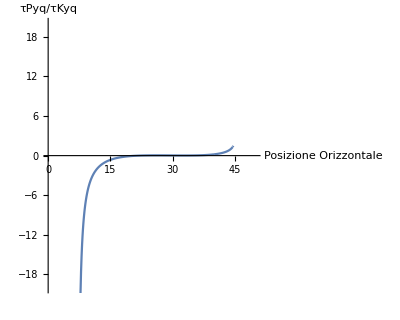

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},ParametricPlot[{Pol3[q][[2,1]],τPyq/τKyq},{q,qmin,qmax},PlotRange->{{0,50},{-20,20}},AxesLabel->{"Posizione Orizzontale","τPyq/τKyq"}]]
```

```mathematica
τPxq=D[Pol3[q][[2,1]], q];
```

```mathematica
τKxq=D[Pol4[q][[2,1]], q];
```

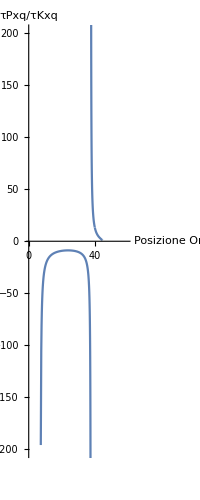

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},ParametricPlot[{Pol3[q][[2,1]],τPxq/τKxq},{q,qmin,qmax},PlotRange->{{0,60},{-200,200}},AxesLabel->{"Posizione Orizzontale","τPxq/τKxq"}]]
```

## Analisi di Accelerazione

Velocità Orizzontale Costante

```mathematica
xP'== τPxq q';
q'== cost/τPxq;
q''== D[q, t];
q''==cost q' D[cost/τPxq, q] ;
```

```mathematica
cost=1;
```

```mathematica
dq1=cost/τPxq;
```

```mathematica
dq2=cost dq1 D[(cost/τPxq), q];
```

Accelerazione Orizzontale Contrappeso

quello fatto da me

```mathematica
pXK''==τKxq q''+(D[τKxq, q])q'^2;
```

```mathematica
dpXK2=τKxq dq2+(D[τKxq, q])(dq1)^2;
```

```mathematica
pYK''==τKyq q''+(D[τKyq, q])q';
```

```mathematica
dpYK2=τKyq dq2+(D[τKyq, q])(dq1)^2;
```

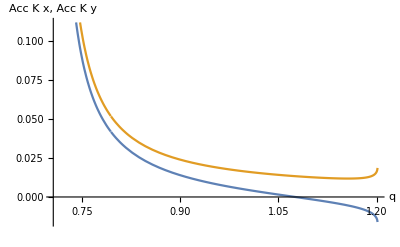

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Plot[{dpXK2,dpYK2},{q,qmin,qmax},AxesLabel->{"q","Acc K x, Acc K y"}]]
```

Il Grafico potrebbe essere in effetti corretto perche il peso esegue una traiettoria a circonferenza

Rapporto di velocità di θ6

```mathematica
τθ6=D[Pol1[q][[1]], q];
```

```mathematica
d2θ6=τθ6 dq2+dq1^2 D[τθ6, q];
```

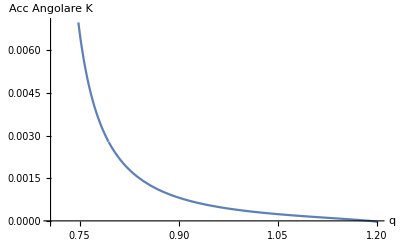

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},Plot[{d2θ6},{q,qmin,qmax},AxesLabel->{"q","Acc Angolare K"}]]
```

## Animazione

```mathematica
Manipulate[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},
	Show[
		ParametricPlot[{{Pol3[q][[2,1]],Pol3[q][[2,2]]},{Pol4[q][[2,1]],Pol4[q][[2,2]]}},{q,qmin,qmax},PlotStyle->Directive[Black,Dashed],PlotRange->{{-30,50},{0,50}}],
		ListPlot[{Pol1[q][[3]],Pol2[q][[3]],Pol3[q],Pol4[q]},Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-30,50},{0,50}}]]],{q,0,π/2}]
```

## Configurazioni Singolari

#### Equazione di Chiusura

```mathematica
eq1x=(Lv1+Lv3)Cos[θ1]+Lv4 Cos[θ4]+Lv5 Cos[θ5]+Lv6 Cos[θ6]+Lv0 Cos[θ0];
eq1y=(Lv1+Lv3)Sin[θ1]+Lv4 Sin[θ4]+Lv5 Sin[θ5]+Lv6 Sin[θ6]+Lv0 Sin[θ0];
eq2x=Lv1 Cos[θ1]+Lv2 Cos[θ2]+Lv6 Cos[θ6]-Lv0 Cos[θ0];
eq2y=Lv1 Sin[θ1]+Lv2 Sin[θ2]+Lv6 Sin[θ6]-Lv0 Sin[θ0];
```

```mathematica
jak={{D[eq1x, θ2],D[eq1x, θ4],D[eq1x, θ5],D[eq1x, θ6]},{D[eq1y, θ2],D[eq1y, θ4],D[eq1y, θ5],D[eq1y, θ6]},{D[eq2x, θ2],D[eq2x, θ4],D[eq2x, θ5],D[eq2x, θ6]},{D[eq2y, θ2],D[eq2y, θ4],D[eq2y, θ5],D[eq2y, θ6]}};
```

```mathematica
jak
```

{{0,-Lv4 Sin[θ4],-Lv5 Sin[θ5],-Lv6 Sin[θ6]},{0,Lv4 Cos[θ4],Lv5 Cos[θ5],Lv6 Cos[θ6]},{-Lv2 Sin[θ2],0,0,-Lv6 Sin[θ6]},{Lv2 Cos[θ2],0,0,Lv6 Cos[θ6]}}

```mathematica
FullSimplify[Det[jak]]
```

Lv2 Lv4 Lv5 Lv6 Sin[θ4-θ5] Sin[θ2-θ6]

```mathematica
sol=Timing@Solve[Det[jak]==0,{θ2,θ4,θ5,θ6},Reals]
```

{0.21875,{{θ5→ConditionalExpression[θ4-2 π C[1],C[1]∈ℤ]},{θ5→ConditionalExpression[-π+θ4-2 π C[1],C[1]∈ℤ]},{θ6→ConditionalExpression[θ2-2 π C[1],C[1]∈ℤ]},{θ6→ConditionalExpression[-π+θ2-2 π C[1],C[1]∈ℤ]}}}

```mathematica
soldef=sol/.C[1]->0
```

{0.21875,{{θ5→θ4},{θ5→-π+θ4},{θ6→θ2},{θ6→-π+θ2}}}

```mathematica
tablesol1=Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0},Table[{eq1x,eq1y,eq2x,eq2y}/.soldef[[2,1]]/.soldef[[2,i]],{i,3,4}]]
```

{{-7.5+36. Cos[θ1]+6.6 Cos[θ2]+39.1 Cos[θ4],13.+36. Sin[θ1]+6.6 Sin[θ2]+39.1 Sin[θ4],7.5+12.2 Cos[θ1]+20.3 Cos[θ2],-13.+12.2 Sin[θ1]+20.3 Sin[θ2]},{-7.5+36. Cos[θ1]-6.6 Cos[θ2]+39.1 Cos[θ4],13.+36. Sin[θ1]-6.6 Sin[θ2]+39.1 Sin[θ4],7.5+12.2 Cos[θ1]+7.1 Cos[θ2],-13.+12.2 Sin[θ1]+7.1 Sin[θ2]}}

```mathematica
tablesol2=Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0},Table[{eq1x,eq1y,eq2x,eq2y}/.soldef[[2,2]]/.soldef[[2,i]],{i,3,4}]]
```

{{-7.5+36. Cos[θ1]+6.6 Cos[θ2]-28.7 Cos[θ4],13.+36. Sin[θ1]+6.6 Sin[θ2]-28.7 Sin[θ4],7.5+12.2 Cos[θ1]+20.3 Cos[θ2],-13.+12.2 Sin[θ1]+20.3 Sin[θ2]},{-7.5+36. Cos[θ1]-6.6 Cos[θ2]-28.7 Cos[θ4],13.+36. Sin[θ1]-6.6 Sin[θ2]-28.7 Sin[θ4],7.5+12.2 Cos[θ1]+7.1 Cos[θ2],-13.+12.2 Sin[θ1]+7.1 Sin[θ2]}}

```mathematica
sol1min=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol1[[1,i]]==0},{x,qmin}]],{i,1,4}];
```

```mathematica
sol2min=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol1[[2,i]]==0},{x,qmin}]],{i,1,4}];
```

```mathematica
sol3min=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol2[[1,i]]==0},{x,qmin}]],{i,1,4}];
```

```mathematica
sol4min=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol2[[2,i]]==0},{x,qmin}]],{i,1,4}];
```

```mathematica
sol1max=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol1[[1,i]]==0},{x,qmax}]],{i,1,4}];
```

```mathematica
sol2max=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol1[[2,i]]==0},{x,qmax}]],{i,1,4}];
```

```mathematica
sol3max=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol2[[1,i]]==0},{x,qmax}]],{i,1,4}];
```

```mathematica
sol4max=Timing@Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD,Lv0=L0,θ1=x,θ2=Pol1[x][[1]],θ4=Pol2[x][[1]]},
		FindRoot[{tablesol2[[2,i]]==0},{x,qmax}]],{i,1,4}];
```

```mathematica
TableForm[{sol1min,sol2min,sol3min,sol4min,sol1max,sol2max,sol3max,sol4max}]
```

0.15625 | x→0.90929
x→0.68276-3.19482×10^-15 ⅈ
x→0.367049+0.367326 ⅈ
x→0.821198
0.109375 | x→0.705888
x→0.674436-4.62853×10^-15 ⅈ
x→1.61252+1.02294×10^-16 ⅈ
x→1.15365
0.109375 | x→1.06688
x→0.279669+0.230121 ⅈ
x→0.367049+0.367326 ⅈ
x→0.821198
0.09375 | x→1.16674
x→3.65522
x→1.61252+1.02294×10^-16 ⅈ
x→1.15365
0.09375 | x→0.90929
x→1.20368+4.79267×10^-15 ⅈ
x→0.367049+0.367326 ⅈ
x→0.821198
0.125 | x→0.705888
x→1.20357+4.45094×10^-15 ⅈ
x→1.61252
x→1.15365
0.109375 | x→1.06688
x→0.279669+0.230121 ⅈ
x→0.367049+0.367326 ⅈ
x→0.821198
0.0625 | x→1.16674
x→0.422426+0.317199 ⅈ
x→1.61252
x→1.15365

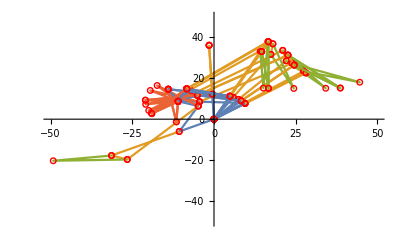

```mathematica
Show[Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol1min[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}],
Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol2min[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}],
Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol3min[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}],
Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol4min[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}]
]
```

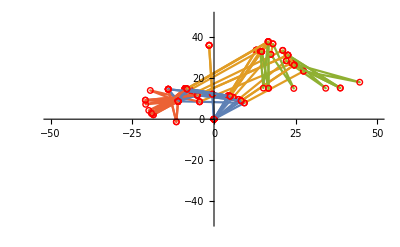

```mathematica
Show[Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol1max[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}],
Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol2max[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}],
Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol3max[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}],
Table[Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD}, ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol4max[[2,i]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-50,50},{-50,50}}]],{i,4}]
]
```

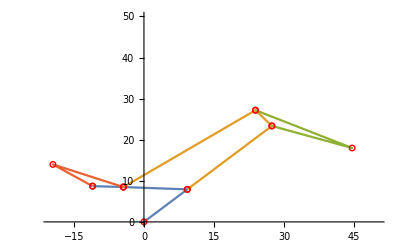

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},
	ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol2min[[2,1]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-20,50},{0,50}}]]
```

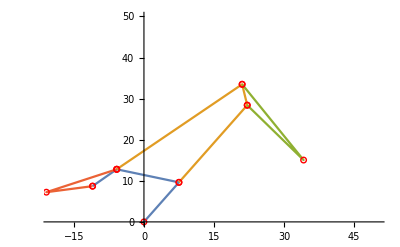

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},
	ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol1min[[2,1]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-20,50},{0,50}}]]
```

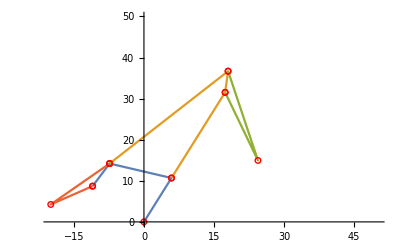

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},
	ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol3max[[2,1]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-20,50},{0,50}}]]
```

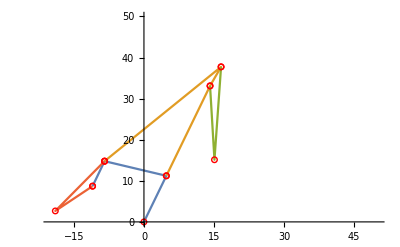

```mathematica
Block[{Lv1=L1,Lv2=L2,Lv3=L3,Lv4=L4,Lv5=L5,Lv6=L6,xvD=xD,yvD=yD},
	ListPlot[{Pol1[x][[3]],Pol2[x][[3]],Pol3[x],Pol4[x]}/.sol4max[[2,1]],Joined->True,PlotMarkers->{Style["○",Red],Medium}, PlotRange->{{-20,50},{0,50}}]]
```